# Test Null vMF Sigma

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

```mathematica
Run["clang++ -I include test/NDFs/test_vMF_sigma.cpp -O3 -o test/NDFs/test_vMF_sigma"]
```

0

```mathematica
roughness="1.2";
du=0.01;
```

```mathematica
argstr=roughness<>" "<>ToString[du]<>" > test/NDFs/vMF.txt"
```

1.2 0.01 > test/NDFs/vMF.txt

```mathematica
Run["./test/NDFs/test_vMF_sigma "<>argstr]
```

0

```mathematica
check=Import["test/NDFs/vMF.txt","Table"];
```

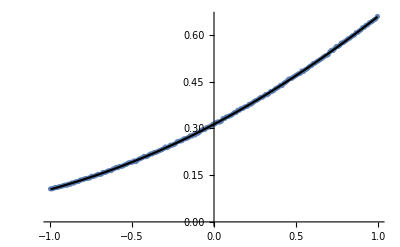

```mathematica
Show[
ListPlot[ plotpoints[check[[2]],du,-1]],
ListLinePlot[plotpoints[check[[1]],du,-1],PlotStyle->Black]
]
```